## Topic

### Definition / Theorem

This is text.

#### Example

## Limit of a complex function

```mathematica
ClearAll[g]
g[z_]:=(z+2)/(z-1)
Limit[g[z],z->Infinity]
Apart[g[z],z]
(*Abs[.99+.01I]*)
Abs[g[1.01]-1]
```

1

1+3/(-1+z)

300.

## Gamma Function

```mathematica
ClearAll[gamma]
(*gamma[s_]:=Integrate[x^(s-1)ⅇ^-x,{x,0,Infinity}]*)
gamma[x_]:=Integrate[t^(x-1)ⅇ^-t,{t,0,Infinity}]
gamma2[x_]:=1/x Integrate[t^x ⅇ^-t,{t,0,Infinity}]
gamma[t]//TraditionalForm
Log[10.,Gamma[70]]
```

Integrate::idiv: Integral of ⅇ^-t t^(-1+t) does not converge on {0,∞}.

∫_0^∞ ⅇ^-t t^(t-1)ⅆt

98.2333

2.54926

2.54926

120

2.54926

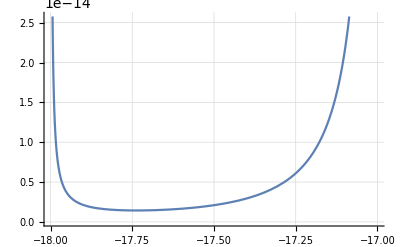

```mathematica
gamma[3.25]//N
gamma2[3.25]//N
gamma[6]
Gamma[3.25]//N
Plot[Gamma[x],{x,-18,-17},GridLines->Automatic]
```

```mathematica
gamma[z_]:=Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]
gamma[z]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[t^(z-1)-ⅇ^-t,{t,0,Infinity}]+Integrate[ⅇ^-t(z-1)t^(z-2),{t,0,Infinity}]
```

Integrate::idiv: Integral of -ⅇ^-t+t^(-1+z) does not converge on {0,∞}.

ConditionalExpression[Gamma[z]+∫_0^∞ (-ⅇ^-t+t^(-1+z))ⅆt, Re[z]>1]

```mathematica
1/6-5/66
```

1/11

```mathematica
D[ -x Cos[x]+Sin[x],{x,1}]//FullSimplify
```

x Sin[x]

```mathematica
Integrate[Gamma[z],z]
```

∫Gamma[z]ⅆz

```mathematica
Integrate[Exp[-a u^2],{u,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √a), Re[a]>0]

```mathematica
Integrate[ⅇ^((z-1)Log[t]-t),{t,0,Infinity}]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
Gamma[I]//N
```

-0.15495-0.498016 ⅈ

```mathematica
Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]/.z:>5
```

24

```mathematica
u[t_]:=t^(z-1)
u[t_]:=1
v[t_]:=-ⅇ^-t
```

```mathematica
Integrate[u[t]D[v[t],{t,1}],{t,0,Infinity}]

Integrate[v[t]D[u[t],{t,1}],{t,0,Infinity}]
```

1

0

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
D[ⅇ^-t t^(x-1),{x,3}]
```

```mathematica
Gamma'''[x]
Integrate[ⅇ^-t t^(-1+x) Log[t]^3,{x,0,Infinity}]
```

Gamma[x] PolyGamma[0,x]^3+3 Gamma[x] PolyGamma[0,x] PolyGamma[1,x]+Gamma[x] PolyGamma[2,x]

ConditionalExpression[-(ⅇ^-t Log[t]^2)/t, Re[Log[t]]<0]

```mathematica
240*.35
```

84.

```mathematica
Solve[{Gamma'[x]==1},x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Gamma[x] PolyGamma[0,x]==1},x]

```mathematica
f[y_]:=Integrate[x Cos[x],x]/.x:>y
f[π]-f[0]
```

-2

```mathematica
Integrate[x Cos[x],{x,0,π}]
```

-2

```mathematica
Table[Residue[Gamma[z],{z,-k}],{k,1,7}]
```

{-1,1/2,-1/6,1/24,-1/120,1/720,-1/5040}

```mathematica
1/(Gamma[z]Gamma[1-z])//FullSimplify
```

Sin[π z]/π

```mathematica
Series[Sin[π z]/π,{z,0,9}]
```

z-(π^2 z^3)/6+(π^4 z^5)/120-(π^6 z^7)/5040+(π^8 z^9)/362880+O[z]^10

```mathematica
Zeta[2];
Denominator[Zeta[6]]
5040/945
```

945

16/3

```mathematica
Zeta[4]
120/90
```

π^4/90

4/3

```mathematica
Zeta[8]
362880/9450
```

π^8/9450

192/5

```mathematica
Integrate[t^(n-1)ⅇ^-t,{t,0,Infinity},Assumptions->n >1 && Element[n,Integers]]
```

Gamma[n]

```mathematica
D[t^(n-1),{t,1}]
```

(-1+n) t^(-2+n)

```mathematica
g[n_]:=-(t^(n-1))ⅇ^-t
Limit[g[n]-g[0],n->Infinity]
```

ConditionalExpression[ⅇ^-t/t, (ⅇ^-t/t|ⅇ^-t)∈ℝ&&Log[t]<0]

```mathematica
Integrate[t^(1-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(2-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(3-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(4-1)ⅇ^-t,{t,0,Infinity}]
```

1

1

2

6

```mathematica
Integrate[t^4 ⅇ^-t,{t,0,Infinity}]
```

24

```mathematica
Limit[(-m ⅇ^-m+1),m->Infinity]
```

1

```mathematica
Product[(2k 2k)/((2k-1)(2k+1)) ,{k,1,Infinity}]
```

π/2

```mathematica
Gamma'[z]/Gamma[z]
```

PolyGamma[0,z]

```mathematica
Series[PolyGamma[0,z],{z,0,6}]
```

-1/z-EulerGamma+(π^2 z)/6+1/2 PolyGamma[2,1] z^2+(π^4 z^3)/90+1/24 PolyGamma[4,1] z^4+(π^6 z^5)/945+1/720 PolyGamma[6,1] z^6+O[z]^7

```mathematica
Series[PolyGamma[1,z],{z,0,6}]
```

1/z^2+π^2/6+PolyGamma[2,1] z+(π^4 z^2)/30+1/6 PolyGamma[4,1] z^3+(π^6 z^4)/189+1/120 PolyGamma[6,1] z^5+(π^8 z^6)/1350+O[z]^7

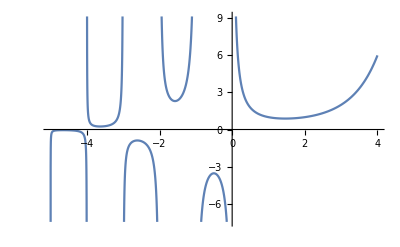

```mathematica
Plot[Gamma[x],{x,-5,4}]
```

```mathematica
Table[{k,Residue[Gamma[z],{z,-k}]},{k,1,7}]//TableForm
```

1 | -1
2 | 1/2
3 | -1/6
4 | 1/24
5 | -1/120
6 | 1/720
7 | -1/5040